```mathematica
SDATA={
CI ->  1.5 10^6 ,(*MPa*)
𝒷->0.380,
𝒹->1.348,
𝒽->0.70 𝒷,
v->2.0 (*m/s*),
IF->0.3 6 3400.0/2(*N*),
k-> 5.0 10^6,
kpneu-> 50.0 10^6,
δ->0.0007392599489560887
};
Wnom =7643.981392287378;(*9.81 939.9*)
Bn =  (CI 𝒷 𝒹)/W(1+5(δ/𝒽))/(1+3(𝒷 /𝒹));
GTR =  0.88 (1-Exp[-0.08 Bn])(1-Exp[-9.5s])+0.032;
MRR=0.9/Bn+0.032+(0.5s)/(√Bn);
NTR = GTR - MRR;
TE = NTR/GTR(1-s);
GT = W GTR;
MR = W MRR;
NT = W NTR;
H = GT v/735.5 ;(*cv*)
```

```mathematica
Simplify@Solve[(π/4  (2 √(δ2(𝒹-δ2)))𝒷  ((kpneu(kpneu+k))/k δ2)==Wnom)//.SDATA,δ2]
```

{{δ2→0.000738275},{δ2→1.348}}

```mathematica
𝒽//.SDATA
```

0.266

```mathematica
Bn//.SDATA/.W->Wnom
```

55.2177

```mathematica
Wnom/9.81
```

779.203

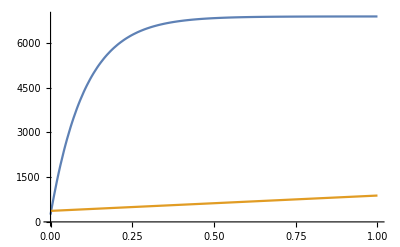

```mathematica
Plot[{GT//.SDATA/.W->Wnom,MR//.SDATA/.W->Wnom},{s,0,1}]
```

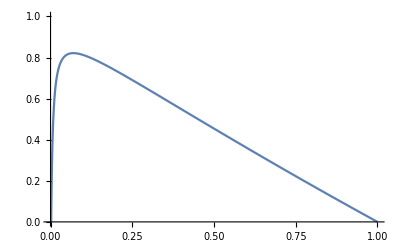

```mathematica
Plot[{TE//.SDATA/.W->Wnom},{s,0,1},PlotRange->{0,1}]
```

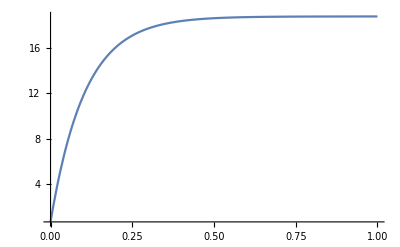

```mathematica
Plot[{H//.SDATA/.W->Wnom},{s,0,1},PlotRange->All]
```

```mathematica
si =s/. FindRoot[D[({TE//.SDATA/.W->Wnom}), s]== 0,{s,0.04}]
```

0.0697711

```mathematica
sol = FindRoot[{D[({TE//.SDATA}), s]== 0,{(NT-IF== 0)//.SDATA}},{{s,si},{W,Wnom+1}}]
```

{s→0.0697711,W→7643.98}

```mathematica
si2=s/.sol;
Wnom2=W/.sol;
```

General::munfl: Exp[-108118.] is too small to represent as a normalized machine number; precision may be lost.

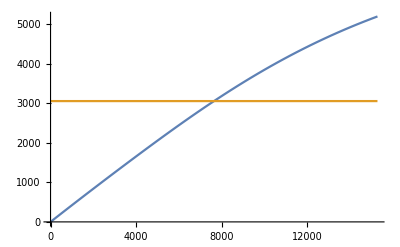

```mathematica
Plot[{NT//.SDATA/.s->si,IF//.SDATA},{W,0,2Wnom2}]
```

```mathematica
Bn//.SDATA/.sol
```

55.2177

```mathematica
GTR//.SDATA/.sol
```

0.453309

```mathematica
NTR//.SDATA/.sol
```

0.400315

```mathematica
GT//.SDATA/.sol
```

3465.08

```mathematica
MR//.SDATA/.sol
```

405.084

```mathematica
NT//.SDATA/.sol
```

3060.

```mathematica
TE//.SDATA/.sol
```

0.821481

```mathematica
H//.SDATA/.sol
```

9.42239